```mathematica
Quit;
ClearAll;
Needs["VariationalMethods`"]
cm=72/2.54;
ConfigureMaTeX["pdfLaTeX"->"/usr/bin/pdflatex","Ghostscript"->"/usr/local/bin/gs"]
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
<<MaTeX`
$HistoryLength=1;
```

ConfigureMaTeX[pdfLaTeX→/usr/bin/pdflatex,Ghostscript→/usr/local/bin/gs]

ConfigureMaTeX::shdw: Symbol "ConfigureMaTeX" appears in multiple contexts {"MaTeX`", "Global`"}; definitions in context "MaTeX`" may shadow or be shadowed by other definitions.

```mathematica
Action=Sqrt[r[x]^2(r[x]^2+2r'[x]v'[x]-(r[x]^2-m[v[x]]/r[x])v'[x]^2)]; (*Action functional (eqn4.5)*)
```

```mathematica
FullSimplify[Eliminate[{EulerEquations[Action,v[x],x],EulerEquations[Action,r[x],x],r[x]^6/r0^4==r[x]^2+2 r'[x] v'[x]-((-m[v[x]])/r[x]+r[x]^2) v'[x]^2},m[v[x]]]] ;(*We can eliminate one of the two EL equations using eqn4.6 which can be derived from reparametrrising the action in terms of v and then minimising*)
```

```mathematica
(*This function does the following: takes arguments r0,t,b,Col, where Col defines the Line colour of the output figures.
1. Produce a inital solution Sol to calculate ℓ/2
2. Produce SolL, i.e. the solution for v,r running from -ℓ/2 to -x0
3. Produce 3 plots of the geodesics in the rx,vx,rv planes, output as a list {rx,vx,rv}
4.Integrate to find geodesic length*)
yL=1;
f[r0_,t_,b_,Col_]:=Module[{a,m0,Eqn1,Eqn2,r,x,v,rmax,xmax,x0,Sol,ℓ,SolL,gr1,gr2,gr3,LInt,dot,scal,gr4,temp1,AH,y,surplot,ab},
a=1/3;
m0=1;
m[v_]:=m0(Tanh[v/a]+1)/2; (*define the mass function*)
Eqn1=r0^4(r[x]^2+2r'[x]v'[x]-(r[x]^2-m[v[x]]/r[x])v'[x]^2)-r[x]^6; 
Eqn2=3 r[x]+r[x]^5/r0^4+(6 r'[x] v'[x])/r[x]-3 r[x] v'[x]^2-2 v''[x];
rmax=100;
x0=1/3 r0^2/rmax^3;
xmax=100;
Sol=NDSolve[{Eqn1==0,Eqn2==0,r[x0]==rmax,v[x0]==t-1/rmax,v'[x0]==-rmax^2/r0^2+b/r0^2},{r,v},{x,x0,xmax}];
ℓ=2*x/.Last[Quiet[FindMinimum[v[x]/.Sol,{x,x0,x0,xmax}]]];
SolL=NDSolve[{Eqn1==0,Eqn2==0,r[-ℓ/2]==rmax,v[-ℓ/2]==t-1/rmax,v'[-ℓ/2]==-rmax^2/r0^2+b/r0^2},{r,v},{x,-ℓ/2,-x0},"ExtrapolationHandler"->{Indeterminate &}];
gr1=Plot[{Evaluate[r[x]/.SolL],Evaluate[m[v[x]]^(1/3)/.SolL]},{x,-ℓ/2,ℓ/2},PlotStyle->{Col,{Dashed,Black}},PlotRange->All];
gr2=Plot[Evaluate[v[x]/.SolL],{x,-ℓ/2,ℓ/2},PlotStyle->{Col},PlotRange->All];
gr3=ParametricPlot[{Evaluate[{v[x],r[x]}/.SolL],Evaluate[{v[x],m[v[x]]^(1/3)}/.SolL]},{x,-ℓ/2,-x0},AspectRatio->1/GoldenRatio,PlotRange->All,PlotStyle->{Col,{Black,Dashed}}];
LInt=null;
gr4=ParametricPlot3D[Evaluate[{x,v[x],r[x]}/.SolL],{x,-ℓ/2,-x0},PlotRange->All,PlotStyle->Col];
AH=ParametricPlot3D[Evaluate[{y,v[x],m[v[x]]^(1/3)}/.SolL],{x,-ℓ/2,-x0},{y,-ℓ/2,ℓ/2},PlotRange->All,PlotStyle->{LightBlue,Opacity[0.5]}];(*PlotPoints->10,MaxRecursion->8*)
ab=ParametricPlot3D[Evaluate[{y,x,r[x]}/.SolL],{x,-ℓ/2,-x0},{y,0,yL},PlotRange->All,PlotStyle->None] ;
surplot=Show[{ab},{ab}/.L_Line:>{GeometricTransformation[L,ReflectionTransform[{0,1,0}]]},PlotRange->{{0,yL},{-ℓ/2,ℓ/2},{0,4}}];
{gr1,gr2,gr3,ℓ,LInt,gr4,AH,surplot}
]
```

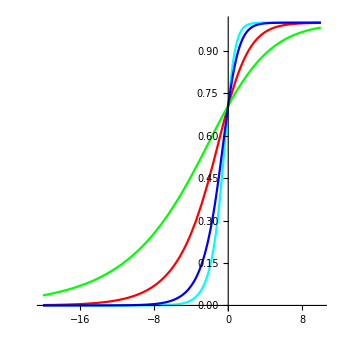

```mathematica
AHloc3=Plot[{((Tanh[x]+1)/2)^(1/2),((Tanh[x/3]+1)/2)^(1/2),((Tanh[x/6]+1)/2)^(1/2),((Tanh[x/1.5]+1)/2)^(1/2)},{x,-20,10},PlotStyle->{{Cyan},{Red},{Green},{Blue}},BaseStyle->texStyle,AxesLabel->MaTeX/@{"v","m(v)^{1/2}"},AxesOrigin->{0,0},ImageSize->12cm,AspectRatio->1]
```

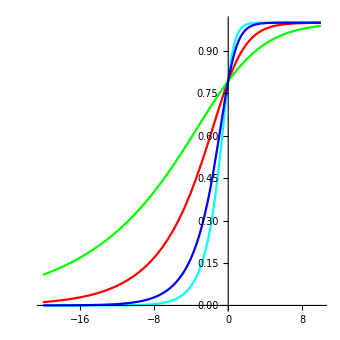

```mathematica
AHloc4=Plot[{((Tanh[x]+1)/2)^(1/3),((Tanh[x/3]+1)/2)^(1/3),((Tanh[x/6]+1)/2)^(1/3),((Tanh[x/1.5]+1)/2)^(1/3)},{x,-20,10},PlotStyle->{{Cyan},{Red},{Green},{Blue}},BaseStyle->texStyle,AxesLabel->MaTeX/@{"v","m(v)^{1/3}"},AxesOrigin->{0,0},ImageSize->12cm,AspectRatio->1]
```

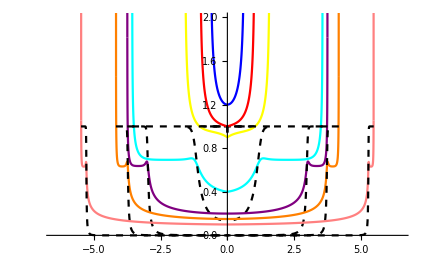

```mathematica
(*Create multiple plots with varying parameters*)
rx1=Part[Quiet[f[1.2,6,0,Blue]],1];
rx2=Part[Quiet[f[1.0,6,0.07,Red]],1];
rx3=Part[Quiet[f[0.9,6,0.165,Yellow]],1];
rx4=Part[Quiet[f[0.4,6,0.635802198,Cyan]],1];
rx5=Part[Quiet[f[0.2,6,0.678605479,Purple]],1];
rx6=Part[Quiet[f[0.15,6,0.68093893,Orange]],1];
rx7=Part[Quiet[f[0.1,6,0.68181948,Pink]],1];
rx8=Part[Quiet[f[0.01,6,0.682037412,Green]],1];
(*Stick the plots together then mirror each plot in the x=0 plane*)
imagerx=Show[{rx1,rx2,rx3,rx4,rx5,rx6,rx7,rx8},{rx1,rx2,rx3,rx4,rx5,rx6,rx7,rx8}/.L_Line:>{GeometricTransformation[L,ReflectionTransform[{1,0}]]},PlotRange->{{-6.5,6.5},{0.0,2.0}},AxesOrigin->{0,0},BaseStyle->texStyle,AxesLabel->MaTeX/@{"$x$","$r$"},AxesOrigin->{0,0},ImageSize->15cm]
```

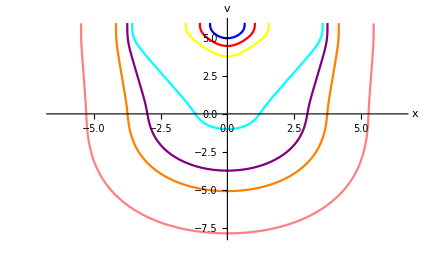

```mathematica
vx1=Part[Quiet[f[1.2,6,0,Blue]],2];
vx2=Part[Quiet[f[1.0,6,0.07,Red]],2];
vx3=Part[Quiet[f[0.9,6,0.166,Yellow]],2];
vx4=Part[Quiet[f[0.4,6,0.635802198,Cyan]],2];
vx5=Part[Quiet[f[0.2,6,0.678605479,Purple]],2];
vx6=Part[Quiet[f[0.15,6,0.68093893,Orange]],2];
vx7=Part[Quiet[f[0.1,6,0.68181948,Pink]],2];

imagevx=Show[{vx1,vx2,vx3,vx4,vx5,vx6,vx7},{vx1,vx2,vx3,vx4,vx5,vx6,vx7}/.L_Line:>{GeometricTransformation[L,ReflectionTransform[{1,0}]]},PlotRange->{{-6.5,6.5},{-8,6}},AxesOrigin->{0,0},AxesLabel->{"x","v"},BaseStyle->texStyle,AxesLabel->MaTeX/@{"$x$","$v$"},AxesOrigin->{0,0},ImageSize->15cm]
```

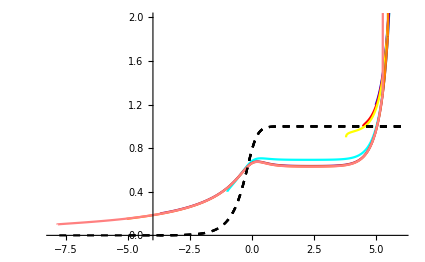

```mathematica
rv1=Part[Quiet[f[1.2,6,0,Blue]],3];
rv2=Part[Quiet[f[1.0,6,0.07,Red]],3];
rv3=Part[Quiet[f[0.9,6,0.166,Yellow]],3];
rv4=Part[Quiet[f[0.4,6,0.635802198,Cyan]],3];
rv5=Part[Quiet[f[0.2,6,0.678605479,Purple]],3];
rv6=Part[Quiet[f[0.15,6,0.68093893,Orange]],3];
rv7=Part[Quiet[f[0.1,6,0.68181948,Pink]],3];

imagerv=Show[{rv1,rv2,rv3,rv4,rv5,rv6,rv7},PlotRange->{{-8,6},{0.0,2.0}},AxesOrigin->{-4,0},BaseStyle->texStyle,AxesLabel->MaTeX/@{"$v$","$r$"},AxesOrigin->{0,0},ImageSize->15cm]
```

```mathematica
xrv1=Part[Quiet[f[1.2,6,0,Blue]],6];
xrv2=Part[Quiet[f[1.0,6,0.07,Red]],6];
xrv3=Part[Quiet[f[0.9,6,0.165,Yellow]],6];
xrv4=Part[Quiet[f[0.4,6,0.635802198,Cyan]],6];
xrv5=Part[Quiet[f[0.2,6,0.678605479,Purple]],6];
xrv6=Part[Quiet[f[0.15,6,0.68093893,Orange]],6];
xrv7=Part[Quiet[f[0.1,6,0.68181948,Pink]],6];
AHP=Part[Quiet[f[0.1,6,0.68181948,Pink]],7];

imagervx=Show[{xrv1,xrv2,xrv3,xrv4,xrv5,xrv6,xrv7},{xrv1,xrv2,xrv3,xrv4,xrv5,xrv6,xrv7}/.L_Line:>{GeometricTransformation[L,ReflectionTransform[{1,0,0}]]},AHP,PlotRange->{{-6,6},{-8,6},{0.0,2.0}},BoxRatios->{1, 1, 1},BaseStyle->texStyle,AxesLabel->MaTeX/@{"$x$","$v$","$r$"},AxesOrigin->{0,0},ImageSize->12cm,AspectRatio->1]
```

-Graphics3D-

```mathematica
Show[Part[Quiet[f[0.1,2,0.656,Pink]],7]]
```

-Graphics3D-

```mathematica
Quiet[Part[f[0.1,6,0.68181948,Pink],8]]
```

-Graphics3D-

```mathematica
Lt0=ListCurvePathPlot[{ {0.40096,-3.56992},{0.605029,-2.35706},{1.48,-0.944},{0.982616,-1.44},{1.16,-1.21319},{2.7756210187132204,-0.493},{3.149860433704435,-0.395},{3.57,-0.33},{4.07611,-0.263066},{75.7,0.00472599},{13.8131,-0.0334017},{5.31,-0.15}},AxesLabel->{"ℓ","Ã(ℓ,t)"},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Green},InterpolationOrder->2];
```

```mathematica
Lt1=ListCurvePathPlot[{{0.405414,-3.49661},{0.62464,-2.19487},{1.19975,-0.871615},{1.42034,-0.610064},{2.824,0.109448},{1.68541,-0.390238},{2.16436,-0.13161},{2.56024,0.0381304},{3.1026,0.184238},{20.75,0.458314},{26.8592,0.489535},{14.0894,0.425324},{12.0519,0.408055},{6.86441,0.33787},{35,0.46}},AxesLabel->{"ℓ","Ã(ℓ,t)"},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Magenta},InterpolationOrder->2];
```

```mathematica
Lt2=ListCurvePathPlot[{ {0.40429,-3.5063},{0.62498,-2.19144},{1.2964,-0.683799},{2.32939,0.523407},{2.80856,0.962405},{3.35641,1.21913},{4.06885,1.3704},{4.344,1.42089},{19.2592,1.64989},{30,1.64989}},AxesLabel->{"ℓ","Ã(ℓ,t)"},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Cyan},InterpolationOrder->2];
```

```mathematica
Lt3=ListCurvePathPlot[{ {0.402377,-3.52357},{0.617944,-2.21982},{2.2305,0.433124},{1.2331,-0.776656},{4.56998,2.7017},{5.41248,2.7972},{6.09171,2.8044},{7.22988,2.84791},{8.81471,2.88957},{21.1478,3.00641},{31,3.01}},AxesLabel->{"ℓ","Ã(ℓ,t)"},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Brown},InterpolationOrder->2];
```

```mathematica
Lt4=ListCurvePathPlot[{ {0.40429,-3.506239},{0.62498,-2.19143},{1.296502,-0.683441},{2.05701,0.246436},{5.70962,3.98875},{6.65742,4.19398},{7.66833,4.22977},{11.6484,4.29879},{19.9156,4.3779},{30,4.3779}},AxesLabel->{"ℓ","Ã(ℓ,t)"},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Purple},InterpolationOrder->2];
```

```mathematica
Lt5=ListCurvePathPlot[{ {0.402377,-3.52357},{0.617944,-2.21982},{1.22165,-0.794287},{2.13691,0.332945},{7.39282,5.6225},{8.55402,5.62957},{8.67754,5.62631},{9.05781,5.63938},{16.0289,5.74634},{30.0289,5.84634}},AxesLabel->{"ℓ","Ã(ℓ,t)"},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Pink},InterpolationOrder->2];
```

```mathematica
Lt6=ListCurvePathPlot[{ {0.402377,-3.52357},{0.62498,-2.19143},{1.28,-0.683441},{2.057,0.246436},{4.97172,3.28971},{8.75,6.99062},{10.94,7.03916},{30,7.13},{8.987,6.886}},AxesLabel->{"ℓ","Ã(ℓ,t)"},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Red},InterpolationOrder->2];
```

```mathematica
Lt7=ListCurvePathPlot[{ {0.406622,-3.4889567476347167},{0.623559,-2.19713},{1.36947,-0.58012},{2.9638,1.19304},{10.24,8.39704},{11.4056,8.41861},{14.6727,8.46855},{30,8.5}},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Orange},InterpolationOrder->2];
```

```mathematica
Lt8=ListCurvePathPlot[{ {0.40429,-3.50629},{0.62498,-2.19143},{1.2965,-0.683441},{2.23052,0.433176},{5.67,3.99811},{35,9.97537},{20,9.975},{9.937159065986817,8.09},{11.34,9.371},{14.2004,9.83473},{12.03,9.586}},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Blue},InterpolationOrder->2];
```

```mathematica
(*Complile all graphs*)
(*numerically solve for AdS4-Schwarzchild thermal result*)
m1=1;
rmax2=100;
Action=Sqrt[r^2/(r^2-m1/r)+r^4 x'[r]^2];
A[ra_]:=2yL(NIntegrate[Action/.NDSolve[{x'[r]==√(ra^4/(r^2(r^2-m1/r)(r^4-ra^4))),x[rmax2]==0.01},x,{r,ra,rmax2}],{r,ra,rmax2}]-rmax2)
q[ra_]:=2yL*Abs[x[ra]/.NDSolve[{x'[r]==√(ra^4/(r^2(r^2-m1/r)(r^4-ra^4))),x[rmax2]==0.01},x,{r,ra,rmax2}]]
TherTable=Quiet[Partition[Flatten[Table[{q[ra],A[ra]},{ra,1,15,0.1}],2],2]];
TherRes=ListLinePlot[{TherTable},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Black,Dashed}];
VacRes=Plot[yL(-(4Pi/q)(Gamma[3/4]/Gamma[1/4])^2),{q,0,60},PlotStyle->{Black, DotDashed},PlotRange->All];
```

```mathematica
Avsl=Show[{VacRes,TherRes,Lt0,Lt1,Lt2,Lt3,Lt4,Lt5,Lt6,Lt7,Lt8},PlotRange->{{0,28},{-5,15}},BaseStyle->texStyle,AxesLabel->MaTeX/@{"\\ell","$\~A$(\\ell,t)"},AxesOrigin->{0,0},ImageSize->12cm,AspectRatio->1,AspectRatio->1]
```

-Graphics-

InterpolatingFunction[{{0., 8.}}, <>]

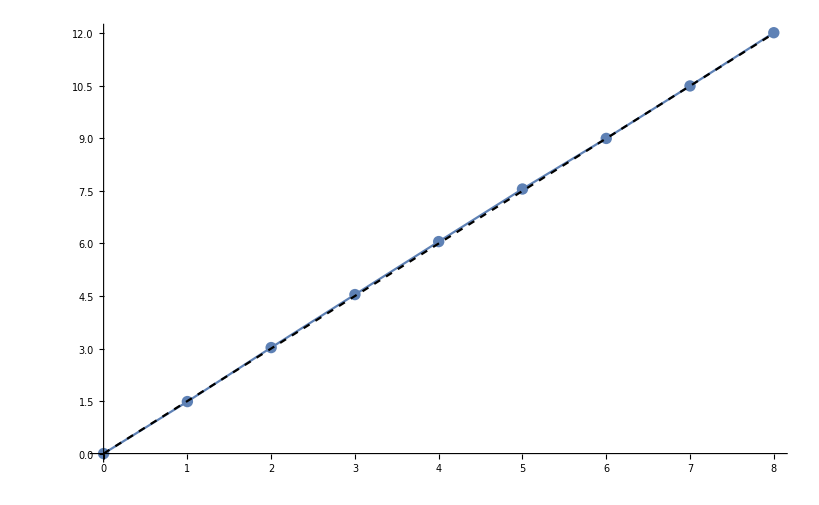

```mathematica
aw=Interpolation[{{0,0},{1,1.485},{2,3.027},{3,4.541},{4,6.054},{5,7.556},{6,9.001},{7,10.5},{8,12.02}}]
Show[ListPlot[aw,PlotStyle->PointSize[0.01]],ListLinePlot[aw],Plot[1.5t,{t,0,8},PlotStyle->{Dashed,Black}]]
```

```mathematica
FindFit[{{0,0},{1,1.485},{2,3.027},{3,4.541},{4,6.054},{5,7.556},{6,9.081},{7,10.59},{8,12.02}},a*x,a,x]
```

{a→1.50948}

```mathematica
bw=aw'
```

InterpolatingFunction[{{0., 8.}}, <>]

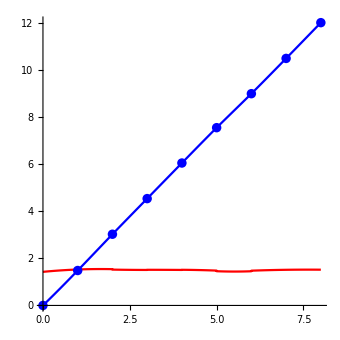

```mathematica
rq=Show[Plot[Evaluate[{aw[x],bw[x]}],{x,0,8},PlotStyle->{Blue,Red}],ListPlot[aw,PlotStyle->{PointSize[0.02],Blue}],BaseStyle->texStyle,AxesLabel->MaTeX/@{"t","\\ell_T"},AxesOrigin->{0,0},ImageSize->12cm,AspectRatio->1,AspectRatio->1]
```

```mathematica
Export["rvads4.png", imagerv]
Export["rxads4.png", imagerx]
Export["vxads4.png", imagevx]
Export["rvxads4.png", imagervx]
```

rvads4.png

rxads4.png

vxads4.png

rvxads4.png

```mathematica
Export["AvslAdS4.png",Avsl]
```

Ahloc.png

AvslAdS4.png

```mathematica
Export["ThermtimesAdS4.png",rq]
```

ThermtimesAdS4.png

```mathematica
Export["Ahloc3.png",AHloc3]
```

Ahloc3.png

```mathematica
Export["Ahloc4.png",AHloc4]
```

Ahloc4.png